```mathematica
weights = <|"a"->2,"b"->20,"c"->14,"d"->7,"e"->4,"f"->19,"g"->12,"h"->8,"i"->1,"j"->13,"k"->16,"l"->5,"m"->17,"n"->15,"o"->18,"p"->9,"q"->10,"r"->3,"s"->11,"t"->6|>
```

<|a→2,b→20,c→14,d→7,e→4,f→19,g→12,h→8,i→1,j→13,k→16,l→5,m→17,n→15,o→18,p→9,q→10,r→3,s→11,t→6|>

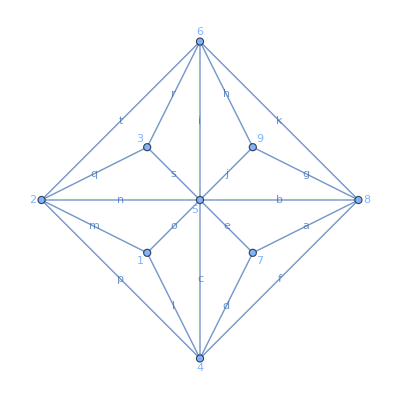

```mathematica
spanningTreesGraph=EdgeTaggedGraph[
Range[9],
{
7<->8, 8<->5, 5 <->4, 4<->7, 7<->5, 4<->8, 8<->9, 9<->6, 6<->5, 5<->9, 8<->6, 1<->4, 1<->2, 2<->5, 1<->5, 2<->4, 2<->3, 3<->6, 3<->5, 2<->6
}->CharacterRange["a","t"],
EdgeWeight->Values[weights],
EdgeLabels->"EdgeTag",VertexLabels->"Name",GraphLayout->{"TutteEmbedding","Rotation"->90Degree}
]
```

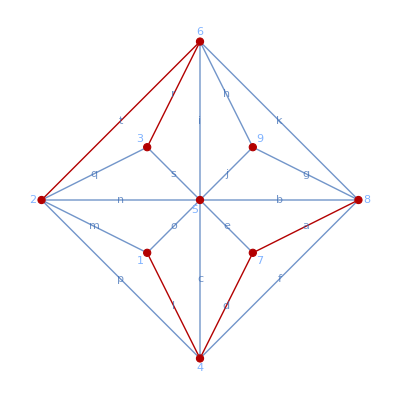

```mathematica
HighlightGraph[spanningTreesGraph, FindSpanningTree[spanningTreesGraph]]
```

```mathematica
edges = EdgeTags[FindSpanningTree[spanningTreesGraph]]
sortedEdges = KeySelect[weights, MemberQ[edges, #] &]//Sort
```

{l,t,r,d,i,e,h,a}

<|i→1,a→2,r→3,e→4,l→5,t→6,d→7,h→8|>

Shown here is helper for Kruskal’s Algorithm

<|d→1,l→2,n→3,m→4,h→5,f→6,g→7,q→11|>

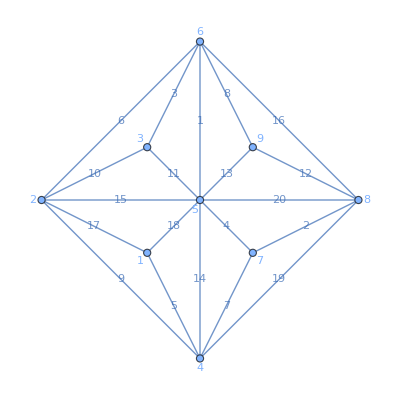

```mathematica
primSpanningTreeGraph = EdgeTaggedGraph[
Range[9],
{
7<->8, 8<->5, 5 <->4, 4<->7, 7<->5, 4<->8, 8<->9, 9<->6, 6<->5, 5<->9, 8<->6, 1<->4, 1<->2, 2<->5, 1<->5, 2<->4, 2<->3, 3<->6, 3<->5, 2<->6
}->CharacterRange["a","t"],
EdgeWeight->Values[weights],
EdgeLabels->"EdgeWeight",VertexLabels->"Name",GraphLayout->{"TutteEmbedding","Rotation"->90Degree}
]
```

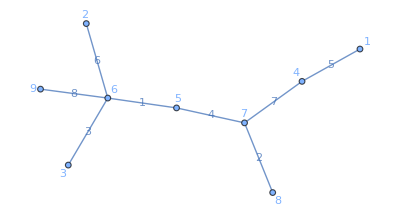

```mathematica
Graph[FindSpanningTree[primSpanningTreeGraph], GraphLayout->"SpringEmbedding"]
```

```mathematica
edges = EdgeTags[FindSpanningTree[primSpanningTreeGraph]]
```

{l,t,r,d,i,e,h,a}

```mathematica
weightedEdges = KeySelect[weights, MemberQ[edges, #] &]//Sort
```

<|i→1,a→2,r→3,e→4,l→5,t→6,d→7,h→8|>